# Dpp gradient modeling in Mathematica

Clear the workspace:

```mathematica
ClearAll["Global`*"]
```

## Diffusion with no consumption (“source-sink” model)

Solving the diffusion equation, ∂_t m == δ ∂_(x,x) m, for steady-state by setting ∂_t m = 0, we turn the problem into an ODE, which is easily solved by the DSolve command.

The steady-state equation, with diffusion coefficient δ:

```mathematica
eqn={0== δ  m''[x]}
```

{0==δ m''[x]}

Specify the boundary conditions. We will specify a constant flux (j) at the left boundary and a sink at the right boundary:

```mathematica
bc = {m'[0]==-j, m[L]==0}
```

{m'[0]==-j,m[L]==0}

Combine the differential equation with the boundary conditions:

```mathematica
fullsystem = Join[eqn,bc]
```

{0==δ m''[x],m'[0]==-j,m[L]==0}

Compute the steady-state solution:

```mathematica
sol=DSolve[fullsystem,m[x],{x}]//Flatten//FullSimplify
```

{m[x]→j (L-x)}

Note that the steady-state solution is just a line (as shown in the plot below), and doesn’t depend on the diffusion coefficient δ. δ only affects the time to reach steady-state (which we are not computing here).

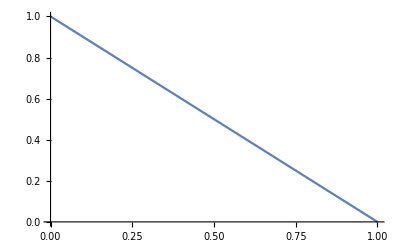

```mathematica
Plot[m[x]/.sol/.{j->1,L->1},{x,0,1}]
```

Note that the amplitude of the gradient (x == 0) is j*L ; i.e., it is both proportional to j and L.

## Diffusion with uniform consumption

Now, let’s calculate the steady-state solution for a morphogen-gradient subjected to uniform consumption (with rate constant α) throughout the field:

```mathematica
eqn={0== δ m''[x]-α m[x]}
```

{0==-α m[x]+δ m''[x]}

Specify the boundary conditions. Later, we will set L -> ∞ so that the boundary condition at x == L doesn’t matter (in order to avoid boundary effects):

```mathematica
bc={m'[0]==-j,m[L]==0}
```

{m'[0]==-j,m[L]==0}

```mathematica
fullsystem=Join[eqn,bc]
```

{0==-α m[x]+δ m''[x],m'[0]==-j,m[L]==0}

```mathematica
sol = DSolve[fullsystem,m[x],{x}]//Flatten//FullSimplify
```

{m[x]→(j √δ Sech[(L √α)/(√δ)] Sinh[((L-x) √α)/(√δ)])/(√α)}

Define λ = √(δ/α)

```mathematica
sol={m[x]->(m[x]/.sol/.δ->λ^2 α)}//FullSimplify
```

{m[x]→j λ Sech[L/λ] Sinh[(L-x)/λ]}

Specify that λ and L are always positive:

```mathematica
parameterConstraints = {λ>0,L>0}
```

{λ>0,L>0}

Calculate the amplitude m(x==0):

```mathematica
amplitude={A-> Limit[j λ Sech[L/λ] Sinh[(L-x)/λ],x->0,Assumptions->parameterConstraints]}//FullSimplify
```

{A→j λ Tanh[L/λ]}

To determine how the amplitude changes as L is increased, take the derivative of the amplitude with respect to L:

```mathematica
dAdL = D[A/.amplitude,L]
```

j Sech[L/λ]^2

Note that ∂_L Ais always positive, since j>0 by definition, and the second term is squared. Thus, the amplitude is increases as L is increased. To show that this effect assymptotes for large values of L, show that  ∂_L A →0 as L → ∞:

```mathematica
Limit[dAdL,L->Infinity,Assumptions->parameterConstraints]
```

0

Define a replacement rule to obtain a solution which includes the term ‘A’ as the amplitude:

```mathematica
amplitudeRR =Solve[A== (A/.amplitude),j]//Flatten//FullSimplify
```

{j→(A Coth[L/λ])/λ}

```mathematica
sol = {m[x]-> (m[x]/.sol/.amplitudeRR)}//FullSimplify
```

{m[x]→A Csch[L/λ] Sinh[(L-x)/λ]}

Plotting this solution reveals that it looks a lot like a decaying exponential, except near the boundary (due to “boundary effects” arising from the presence of the sink there):

```mathematica
parameters = {A->1,λ->0.3,L->1}
```

{A→1,λ→0.3,L→1}

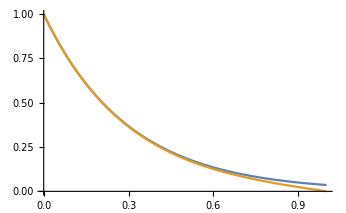

```mathematica
Plot[{ A E^(-x/λ)/.parameters,m[x]/.sol/.parameters},{x,0,1}]
```

To avoid “boundary effects” from the right boundary, set L->∞. Note that, in order to compute the limit, we must tell Mathematica that λ > 0

```mathematica
sol={m[x]-> Limit[m[x]/.sol,L->Infinity,Assumptions->{λ>0}]}
```

{m[x]→A ⅇ^(-x/λ)}

As L->∞, the solution is a decaying exponential (shown in the plot below). And, the amplitude of the gradient is j*λ:

```mathematica
Limit[A/.amplitude,L->Infinity,Assumptions->parameterConstraints]
```

j λ

## Two-domain reaction-diffusion model

In the case of Dpp in the wing disc, Spalt inhibits the expression of Dpp’s receptor, so that λ is greater within the Spalt domain (the “proximal domain”) than beyond the Spalt boundary (the “distal domain”). Let’s model this as if each domain had distinct degradation rate constants: αp being the degradation rate constant within the proximal domain and αd being that within the distal domain.

```mathematica
eqnProx={0==δp m''[x]-αp m[x]}
```

{0==-αp m[x]+δp m''[x]}

```mathematica
eqnDist={0==δd m''[x]-αd m[x]}
```

{0==-αd m[x]+δd m''[x]}

Define ' xB' as the location of the "interface boundary" between the two domains.

```mathematica
bcProx={m'[0]==-j,m[xB]==mB}
```

{m'[0]==-j,m[xB]==mB}

```mathematica
bcDist={m[xB]==mB,m[L]==0}
```

{m[xB]==mB,m[L]==0}

Define λp = √(δ/αp)and λd = √(δ/αd)

```mathematica
decayLengths = {αp->δp/λp^2 ,αd->δd/λd^2}
```

{αp→δp/λp^2,αd→δd/λd^2}

Define our parameter constraints:

```mathematica
parameterConstraints = {αp>0,αd>0,δp>0,δd>0,λp>0,λd>0,mB>0,m0>0,xB>0}
```

{αp>0,αd>0,δp>0,δd>0,λp>0,λd>0,mB>0,m0>0,xB>0}

```mathematica
eqnProx=FullSimplify[eqnProx/.decayLengths,Assumptions->parameterConstraints]
```

{m[x]==λp^2 m''[x]}

```mathematica
eqnDist=FullSimplify[eqnDist/.decayLengths,Assumptions->parameterConstraints]
```

{m[x]==λd^2 m''[x]}

```mathematica
fullsystemProx=Join[eqnProx,bcProx]
```

{m[x]==λp^2 m''[x],m'[0]==-j,m[xB]==mB}

```mathematica
fullsystemDist=Join[eqnDist,bcDist]
```

{m[x]==λd^2 m''[x],m[xB]==mB,m[L]==0}

```mathematica
solProx=FullSimplify[DSolve[fullsystemProx,m[x],{x}],Assumptions->parameterConstraints]//Flatten
```

{m[x]→Sech[xB/λp] (mB Cosh[x/λp]-j λp Sinh[(x-xB)/λp])}

In solving the equations for the distal domain, we want Mathematica to name the integration constants a different character (other than C), since these integration constants are different from the ones in the proximal domain.

```mathematica
solDist=FullSimplify[DSolve[fullsystemDist,m[x],{x},GeneratedParameters->B],Assumptions->parameterConstraints]//Flatten
```

{m[x]→mB Csch[(L-xB)/λd] Sinh[(L-x)/λd]}

To avoid boundary effects at x == L, set L -> Infinity. Note that the solution in the distal domain becomes a simple decaying exponential.

```mathematica
solDist = {m[x]-> Limit[m[x]/.solDist,L->Infinity,Assumptions->parameterConstraints]}
```

{m[x]→ⅇ^((-x+xB)/λd) mB}

Impose the “continuity condition” that the slopes of the solutions should be the same for both solProx and solDist at the interface boundary:

```mathematica
continuityCondition = FullSimplify[{(D[m[x]/.solProx,x]/.x->xB)==(D[m[x]/.solDist,x]/.x->xB)},Assumptions->parameterConstraints]
```

{j λd λp Sech[xB/λp]==mB (λp+λd Tanh[xB/λp])}

```mathematica
mBsol = FullSimplify[Solve[continuityCondition,mB],Assumptions->parameterConstraints]//Flatten
```

{mB→(j λd λp Sech[xB/λp])/(λp+λd Tanh[xB/λp])}

Substitute for ‘mB’ in our solutions:

```mathematica
solProx=FullSimplify[{m[x]->(m[x]/.solProx/.mBsol)},Assumptions->parameterConstraints]
```

{m[x]→(j λp Sech[xB/λp] (λd Cosh[(x-xB)/λp]-λp Sinh[(x-xB)/λp]))/(λp+λd Tanh[xB/λp])}

```mathematica
solDist=FullSimplify[{m[x]->(m[x]/.solDist/.mBsol)},Assumptions->parameterConstraints]
```

{m[x]→(ⅇ^((-x+xB)/λd) j λd λp Sech[xB/λp])/(λp+λd Tanh[xB/λp])}

Note that, in the distal domain, the solution is simply a decaying exponential (similar to the solution of the model with uniform consumption) with decay length λd, since ‘x’ only appears in the exponent of the exponential. The (j λd λp Sech[xB/λp])/(λp+λd Tanh[xB/λp]) term (=mB) is a constant and constitutes the amplitude of the exponential:

```mathematica
amplitudeDist = {mB-> m[x]/.solDist/.x->xB} //FullSimplify
```

{mB→(j λd λp Sech[xB/λp])/(λp+λd Tanh[xB/λp])}

To calculate the amplitude of the gradient, consider solProx:

```mathematica
amplitudeProx = FullSimplify[{m0-> m[x]/.solProx/.x->0},Assumptions->parameterConstraints]
```

{m0→(j λp (λd+λp Tanh[xB/λp]))/(λp+λd Tanh[xB/λp])}

To determine whether the amplitude of the gradient is predicted to increase or decrease as the location of the interface boundary ‘xB’ is changed, calculate the derivative of the amplitude with respect to xB:

```mathematica
dm0dxB = FullSimplify[D[m0/.amplitudeProx,xB],Assumptions->parameterConstraints]
```

(j (-λd^2+λp^2))/(λp Cosh[xB/λp]+λd Sinh[xB/λp])^2

The denominator, (λp Cosh[xB/λp]+λd Sinh[xB/λp])^2, is always positive due to the squaring. The numerator is positve when λp > λd , and negative when λp < λd. Thus, when λp > λd, the amplitude of the gradient increases monotonically as the location of the interface boundary ‘xB’ increases. Show that the amplitude of the gradient asymptotes for large values of ‘xB’ by showing that the derivative tends to zero:

```mathematica
Limit[dApdxB,xB->Infinity,Assumptions->parameterConstraints]
```

dApdxB

Obtain some replacement rules so that we can substitute for the amplitudes in ‘solProx’ and ‘solDist’

```mathematica
amplitudeDistRR=FullSimplify[Solve[mB==(mB/.amplitudeDist),j],Assumptions-> parameterConstraints]//Flatten
```

{j→(mB Cosh[xB/λp])/λd+(mB Sinh[xB/λp])/λp}

```mathematica
amplitudeProxRR=FullSimplify[Solve[m0==(m0/.amplitudeProx),j],Assumptions-> parameterConstraints]//Flatten
```

{j→(m0 (λp+λd Tanh[xB/λp]))/(λp (λd+λp Tanh[xB/λp]))}

```mathematica
FullSimplify[amplitudeDist/.amplitudeProxRR,Assumptions->parameterConstraints]
```

{mB→(m0 λd Sech[xB/λp])/(λd+λp Tanh[xB/λp])}

```mathematica
solProx =FullSimplify[{m[x]->(m[x]/.solProx/.amplitudeProxRR)},Assumptions->parameterConstraints]
```

{m[x]→(m0 Sech[xB/λp] (λd Cosh[(x-xB)/λp]-λp Sinh[(x-xB)/λp]))/(λd+λp Tanh[xB/λp])}

```mathematica
solDist =FullSimplify[{m[x]-> (m[x]/.solDist/.amplitudeDistRR//FullSimplify)},Assumptions->parameterConstraints]
```

{m[x]→ⅇ^((-x+xB)/λd) mB}

Now, combine ‘solProx’ and ‘solDist’ to make the full solution. Use the ‘UnitStep’ function to specify that ‘solProx’ should be used for x < xB, and ‘solDist’ for x > xB

```mathematica
fullsol =FullSimplify[{ m[x]-> (m[x]/.solProx)UnitStep[-(x-xB)] + (m[x]/.solDist)UnitStep[x-xB]},Assumptions-> parameterConstraints]
```

{m[x]→ⅇ^((-x+xB)/λd) mB UnitStep[x-xB]+(m0 Sech[xB/λp] (λd Cosh[(x-xB)/λp]-λp Sinh[(x-xB)/λp]) UnitStep[-x+xB])/(λd+λp Tanh[xB/λp])}

We can put the solution into a more readable form:

```mathematica
m[x]/.fullsol//TraditionalForm
```

(m0 xB-x sech(xB/λp) (λd cosh((x-xB)/λp)-λp sinh((x-xB)/λp)))/(λd+λp tanh(xB/λp))+mB x-xB ⅇ^((xB-x)/λd)

Plot the solution for a certain set of parameter values:

```mathematica
parameters = {λp->0.5,λd->0.1,xB->1,j->1}
```

{λp→0.5,λd→0.1,xB→1,j→1}

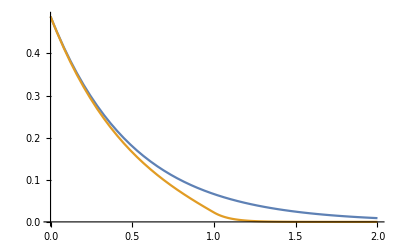

```mathematica
Plot[{m0 E^(-x/λp)/.amplitudeProx/.parameters,m[x]/.fullsol/.amplitudeProx/.amplitudeDist/.parameters},{x,0,2},PlotRange->Full]
```

As a sanity check, the solution should match the exponential when λp == λd

```mathematica
parameters = {λp->0.5,λd->0.5,xB->1,j->1}
```

{λp→0.5,λd→0.5,xB→1,j→1}

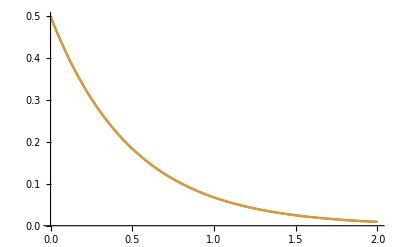

```mathematica
Plot[{m0 E^(-x/λp)/.amplitudeProx/.parameters,m[x]/.fullsol/.amplitudeProx/.amplitudeDist/.parameters},{x,0,2},PlotRange->Full]
```

## Sensitivity analyses

To perform sensitivity analyses let’s solve for the location ‘xB’ as a function of all other parameters, using the continuity condition above. First, let’s replace the flux ‘j’ with the gradient amplitude ‘m0’, so that we can specify uniform consumption and two-domain models having the same amplitudes. This doesn’t effect our results, since, for both the uniform consumption and two-domain gradients, ‘m0’ is linearly proportional ‘j’, and so the sensitivity of the gradient to variations in ‘m0’ is identical to that to variations in ‘j’.

```mathematica
continuityCondition
```

{j λd λp Sech[xB/λp]==mB (λp+λd Tanh[xB/λp])}

```mathematica
continuityConditionAmplitudeSpecified = FullSimplify[continuityCondition/.amplitudeProxRR,Assumptions->parameterConstraints]
```

{m0 λd Sech[xB/λp]==mB (λd+λp Tanh[xB/λp])}

Now, solve for ‘xB’.

```mathematica
xBsolTD = FullSimplify[Solve[continuityConditionAmplitudeSpecified,xB],Assumptions->parameterConstraints]//Flatten
```

{xB→ConditionalExpression[λp (2 ⅈ π C[1]-Log[mB (λd+λp)]+Log[m0 λd-√((m0-mB) (m0+mB) λd^2+mB^2 λp^2)]),C[1]∈Integers],xB→ConditionalExpression[λp (2 ⅈ π C[1]-Log[mB (λd+λp)]+Log[m0 λd+√((m0-mB) (m0+mB) λd^2+mB^2 λp^2)]),C[1]∈Integers]}

```mathematica
xBsolTD = {xBsolTD/.C[1]->0//Last}
```

{xB→λp (-Log[mB (λd+λp)]+Log[m0 λd+√((m0-mB) (m0+mB) λd^2+mB^2 λp^2)])}

This solution corresponds to the two-domain model. Now, solve for ‘xB’ for the uniform consumption model:

```mathematica
xBsolExp=Solve[mB==m0 E^(-xB/λe),xB]//Flatten
```

{xB→ConditionalExpression[λe (2 ⅈ π C[1]+Log[m0/mB]),C[1]∈Integers]}

```mathematica
xBsolExp={xB-> (xB/.xBsolExp/.C[1]->0)}
```

{xB→λe Log[m0/mB]}

With these two solutions, it is relatively straightforward to calculate the sensitivity of ‘xB’ to variations in other parameters.

## Two-domain-gradual-sink model

Now, we will modify the two-domain model so that the strength of the sink increases gradually starting from the interface boundary. The motivation for this model is the observation that the expression of Dpp’s cell-surface receptor Tkv doesn’t appear to increase as a step function at the Sal boundary; rather, it appears to increase gradually starting from the Sal boundary. Let’s model this by assuming that the consumption rate constant of the morphogen increases as a linear function starting from the interface boundary, and the slope of this increase is αm.

```mathematica
eqnProx = {0 ==  δp m''[x] -αp m[x]}
```

{0==-αp m[x]+δp m''[x]}

```mathematica
eqnDist={0 ==  δd m''[x] -(αp+(x-xB)αs) m[x]}
```

{0==-(αp+(x-xB) αs) m[x]+δd m''[x]}

```mathematica
bcProx = {m[0]==m0,m[xB]==mB}
```

{m[0]==m0,m[xB]==mB}

```mathematica
bcDist = {m[xB]==mB,m[L] == 0}
```

{m[xB]==mB,m[L]==0}

Define λp = √(δ/αp) and qs = αs / (λp^2 αp) = αs / δ

```mathematica
decayLengths = {αp-> δp /λp^2,αs-> qs δd}
```

{αp→δp/λp^2,αs→qs δd}

Define the constraints on the parameters. Let’s assume αm (and qm) are greater than zero. (If we let them get less than zero, we risk getting a negative consumption rate constant.)

```mathematica
parameterConstraints={δp>0,δd>0,αp>0,λp>0,0<xB<L,qs>0,ψ> 0,ϕ+xB ψ>0}
```

{δp>0,δd>0,αp>0,λp>0,0<xB<L,qs>0,ψ>0,ϕ+xB ψ>0}

```mathematica
eqnProx=FullSimplify[eqnProx/.decayLengths,Assumptions->parameterConstraints]
```

{m[x]==λp^2 m''[x]}

```mathematica
eqnDist=FullSimplify[eqnDist/.decayLengths,Assumptions->parameterConstraints]
```

{(δp+qs (x-xB) δd λp^2) m[x]==δd λp^2 m''[x]}

```mathematica
Solve[eqnDist,m''[x]]//FullSimplify
```

{{m''[x]→(qs (x-xB)+δp/(δd λp^2)) m[x]}}

Let ϕ = 1/λp^2-xB qs and ψ = qs

```mathematica
lumpedParameters = {ϕ-> 1/λp^2-xB qs,ψ-> qs}
```

{ϕ→-qs xB+1/λp^2,ψ→qs}

```mathematica
lumpedParameters2 = Solve[{ϕ==(ϕ/.lumpedParameters),ψ==(ψ/.lumpedParameters)},{λp,qs}]//Last//FullSimplify
```

{λp→1/(√(ϕ+xB ψ)),qs→ψ}

```mathematica
eqnDist=FullSimplify[eqnDist/.lumpedParameters2,Assumptions->parameterConstraints]
```

{((x-xB) δd ψ+δp (ϕ+xB ψ)) m[x]==δd m''[x]}

```mathematica
fullsystemProx=Join[eqnProx,bcProx]
```

{m[x]==λp^2 m''[x],m[0]==m0,m[xB]==mB}

```mathematica
fullsystemDist=Join[eqnDist,bcDist]
```

{((x-xB) δd ψ+δp (ϕ+xB ψ)) m[x]==δd m''[x],m[xB]==mB,m[L]==0}

```mathematica
solProx =FullSimplify[DSolve[fullsystemProx,m[x],{x}],Assumptions->parameterConstraints]//Flatten
```

{m[x]→Csch[xB/λp] (mB Sinh[x/λp]-m0 Sinh[(x-xB)/λp])}

```mathematica
solDist = FullSimplify[DSolve[fullsystemDist,m[x],{x}],Assumptions->parameterConstraints]//Flatten
```

{m[x]→(mB (-AiryAi[((x-xB) δd ψ+δp (ϕ+xB ψ))/(δd ψ^(2/3))] AiryBi[((L-xB) δd ψ+δp (ϕ+xB ψ))/(δd ψ^(2/3))]+AiryAi[((L-xB) δd ψ+δp (ϕ+xB ψ))/(δd ψ^(2/3))] AiryBi[((x-xB) δd ψ+δp (ϕ+xB ψ))/(δd ψ^(2/3))]))/(AiryAi[((L-xB) δd ψ+δp (ϕ+xB ψ))/(δd ψ^(2/3))] AiryBi[(δp (ϕ+xB ψ))/(δd ψ^(2/3))]-AiryAi[(δp (ϕ+xB ψ))/(δd ψ^(2/3))] AiryBi[((L-xB) δd ψ+δp (ϕ+xB ψ))/(δd ψ^(2/3))])}

```mathematica
solDist ={m[x]-> Limit[m[x]/.solDist,L->Infinity,Assumptions->parameterConstraints]}
```

{m[x]→(mB AiryAi[((x-xB) δd ψ+δp (ϕ+xB ψ))/(δd ψ^(2/3))])/AiryAi[(δp (ϕ+xB ψ))/(δd ψ^(2/3))]}

As before, couple the solutions in the proximal and distal domain using the continuity condition.

```mathematica
continuityCond ={( D[(m[x]/.solProx),x]/.x->xB)==( D[(m[x]/.solDist),x]/.x->xB)}
```

{(-m0/λp+(mB Cosh[xB/λp])/λp) Csch[xB/λp]==(mB ψ^(1/3) AiryAiPrime[(δp (ϕ+xB ψ))/(δd ψ^(2/3))])/AiryAi[(δp (ϕ+xB ψ))/(δd ψ^(2/3))]}

```mathematica
mBsol=FullSimplify[Solve[continuityCond,mB],Assumptions->parameterConstraints]//Flatten
```

{mB→m0/(Cosh[xB/λp]-(λp ψ^(1/3) AiryAiPrime[(ϕ+xB ψ)/ψ^(2/3)] Sinh[xB/λp])/AiryAi[(ϕ+xB ψ)/ψ^(2/3)])}

```mathematica
solProxCoupled=FullSimplify[solProx/.mBsol,Assumptions->parameterConstraints]
```

{m[x]→m0 Csch[xB/λp] (-Sinh[(x-xB)/λp]+Sinh[x/λp]/(Cosh[xB/λp]-(λp ψ^(1/3) AiryAiPrime[(ϕ+xB ψ)/ψ^(2/3)] Sinh[xB/λp])/AiryAi[(ϕ+xB ψ)/ψ^(2/3)]))}

```mathematica
solDistCoupled = FullSimplify[solDist/.mBsol,Assumptions->parameterConstraints]
```

{m[x]→(m0 AiryAi[(ϕ+x ψ)/ψ^(2/3)])/(AiryAi[(ϕ+xB ψ)/ψ^(2/3)] Cosh[xB/λp]-λp ψ^(1/3) AiryAiPrime[(ϕ+xB ψ)/ψ^(2/3)] Sinh[xB/λp])}

```mathematica
solProxCoupled={m[x]-> FullSimplify[m[x]/.solProxCoupled/.lumpedParameters,Assumptions->parameterConstraints]}
```

{m[x]→m0 Csch[xB/λp] (-Sinh[(x-xB)/λp]+Sinh[x/λp]/(Cosh[xB/λp]-(qs^(1/3) λp AiryAiPrime[1/(qs^(2/3) λp^2)] Sinh[xB/λp])/AiryAi[1/(qs^(2/3) λp^2)]))}

```mathematica
solDistCoupled={m[x]-> FullSimplify[m[x]/.solDistCoupled/.lumpedParameters,Assumptions->parameterConstraints]}
```

{m[x]→(m0 AiryAi[(qs (x-xB)+1/λp^2)/qs^(2/3)])/(AiryAi[1/(qs^(2/3) λp^2)] Cosh[xB/λp]-qs^(1/3) λp AiryAiPrime[1/(qs^(2/3) λp^2)] Sinh[xB/λp])}

The full solution:

```mathematica
fullsol =FullSimplify[{ m[x]-> (m[x]/.solProxCoupled)UnitStep[-(x-xB)] + (m[x]/.solDistCoupled)UnitStep[x-xB]},Assumptions-> parameterConstraints]
```

{m[x]→(m0 (AiryAi[(qs (x-xB)+1/λp^2)/qs^(2/3)] UnitStep[x-xB]+(AiryAi[1/(qs^(2/3) λp^2)] Cosh[(x-xB)/λp]+qs^(1/3) λp AiryAiPrime[1/(qs^(2/3) λp^2)] Sinh[(x-xB)/λp]) UnitStep[-x+xB]))/(AiryAi[1/(qs^(2/3) λp^2)] Cosh[xB/λp]-qs^(1/3) λp AiryAiPrime[1/(qs^(2/3) λp^2)] Sinh[xB/λp])}

We can put the solution into a more readable form:

```mathematica
m[x]/.fullsol//TraditionalForm
```

(m0 (x-xB (qs (x-xB)+1/λp^2)/qs^(2/3)+xB-x (1/(qs^(2/3) λp^2) cosh((x-xB)/λp)+λp qs^(1/3) 1/(qs^(2/3) λp^2) sinh((x-xB)/λp))))/(1/(qs^(2/3) λp^2) cosh(xB/λp)-λp qs^(1/3) 1/(qs^(2/3) λp^2) sinh(xB/λp))

Plot the solution for a certain set of parameter values:

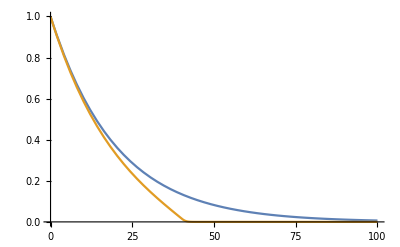

```mathematica
parameters = {λp->20,qs->1,xB->40,m0->1};Plot[{m0 E^(-x/λp)/.parameters,m[x]/.fullsol/.parameters},{x,0,100},PlotRange->Full]
```

As a sanity check, the solution should match the exponential as qm -> 0. Note the effect of qm depends on the value of λp.

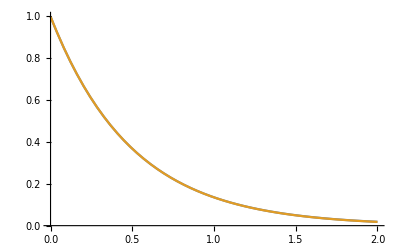

```mathematica
parameters = {λp->0.5,qs->0.1,xB->1,m0->1};Plot[{m0 E^(-x/λp)/.parameters,m[x]/.fullsol/.parameters},{x,0,2},PlotRange->Full]
```